```mathematica
导入一些参数
```

```mathematica
Ωm=0.27;
Ωl=0.73;
Ωk=0;
e[z_]:=√(Ωm(1+z)^3+Ωk(1+z)^2+Ωl);
```

```mathematica
当前epoch下event horizon的红移zH
```

```mathematica
zH=x/.FindRoot[NIntegrate[1/e[z],{z,0,x}]==NIntegrate[1/(a^2 √(Ωm a^-3+Ωl)),{a,1,∞}],{x,2}]
```

NIntegrate::nlim: z = x 不是积分的一个有效的极限.

1.68738

```mathematica
宇宙年龄（Hubble Time为单位）
```

```mathematica
NowAge=NIntegrate[1/((1+z)e[z]),{z,0,∞}]
```

0.992687

```mathematica
求解z[τ]
```

```mathematica
zeq=(Ωm/Ωl)^(-1/3)-1;
Req=(Ωm/Ωl)^(1/3);
h=0.7;

Ht[τ_]:=√Ωl Coth[3/2 √Ωl τ];

Hz[z_]:=√((Cosh[3/2 √Ωl τ])^-2(1+z)^3+(Coth[3/2 √Ωl τ])^-2);

HubbleTime=9.78/h; (*Gy*)
HubbleDistance=3000/h;
```

```mathematica
解方程ODE
```

```mathematica
solve=NDSolve[{z'[τ]==(1+z[τ])√Ωl Coth[3/2 √Ωl τ]-√Ωl Coth[3/2 √Ωl τ]√((Cosh[3/2 √Ωl τ])^-2(1+z[τ])^3+(Coth[3/2 √Ωl τ])^-2),z[NowAge]==1.6873758287034117},z,{τ,NowAge,15NowAge}]
```

{{z→InterpolatingFunction[{{0.992687, 14.8903}}, <>]}}

```mathematica
这是z[τ]的图
```

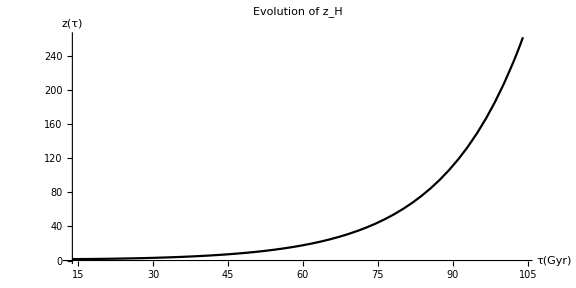

```mathematica
ParametricPlot[{τ HubbleTime, z[τ]/.solve},{τ,NowAge,7.5NowAge},AspectRatio->1/2,ImageSize->Large,PlotRange->Full,PlotStyle->Black,AxesLabel->{HoldForm["τ(Gyr)"],HoldForm["z(τ)"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Automatic},PlotLabel->"Evolution of z_H"]
```

```mathematica
宇宙的尺度因子随时间的变化，横轴是时间(Gyr)，纵轴是scale factor。可以看出宇宙的确在加速膨胀（在这种parameter下）
```

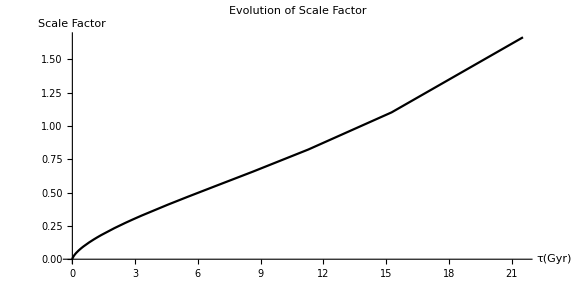

```mathematica
ParametricPlot[{HubbleTime*NIntegrate[1/((1+x)e[x]),{x,z,∞}],1/(1+z)},{z,1000,-0.4},PlotStyle->Black,AspectRatio->1/2,AxesLabel->{HoldForm["τ(Gyr)"],HoldForm["Scale Factor"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Automatic},PlotLabel->"Evolution of Scale Factor"]
```

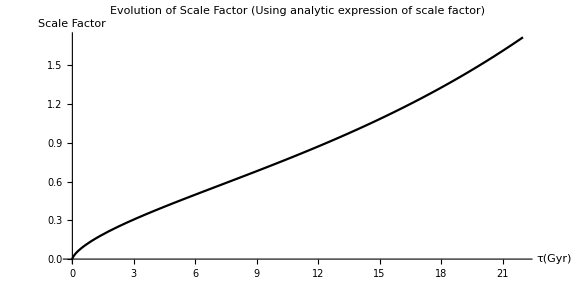

```mathematica
ParametricPlot[{τ HubbleTime,Req(Sinh[3/2 √Ωl τ])^(2/3)},{τ,0,22/HubbleTime},PlotStyle->Black,AspectRatio->1/2,AxesLabel->{HoldForm["τ(Gyr)"],HoldForm["Scale Factor"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Automatic},PlotLabel->"Evolution of Scale Factor \n(Using analytic expression of scale factor)"]
```

```mathematica
第四题
```

```mathematica
这是现在zH处的时间τ'
```

```mathematica
ArcSinh[((1/(1+zH))/Req)^(3/2)]/(3/2 √Ωl)
```

0.284859

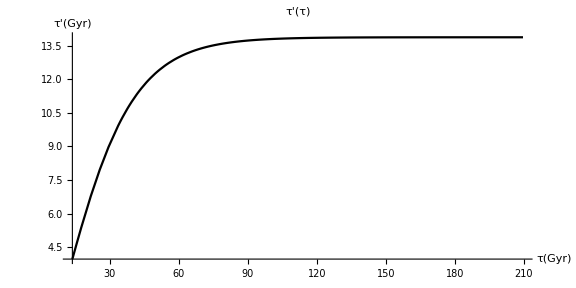

```mathematica
ParametricPlot[{t*HubbleTime,HubbleTime ArcSinh[((1/(1+zH))/Req)^(3/2)]/(3/2 √Ωl)+HubbleTime*NIntegrate[1/(1+z[τ]/.solve),{τ,NowAge,t}]},{t,NowAge,15},PlotRange->Full,AspectRatio->1/2,ImageSize->Large,PlotStyle->Black,AxesLabel->{HoldForm["τ(Gyr)"],HoldForm["τ'(Gyr)"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Automatic},PlotLabel->"τ'(τ)"]
```

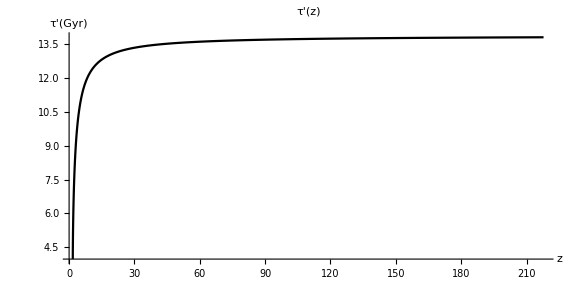

```mathematica
ParametricPlot[{z[t]/.solve⟦1⟧,ArcSinh[((1/(1+zH))/Req)^(3/2)]/(3/2 √Ωl)* HubbleTime+HubbleTime*NIntegrate[1/(1+z[τ]/.solve),{τ,NowAge,t}]},{t,0.9926868741224383,101/HubbleTime},PlotRange->Full,AspectRatio->1/2,ImageSize->Large,PlotStyle->Black,AxesLabel->{HoldForm["z"],HoldForm["τ'(Gyr)"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->All,ImageSize->Large,Ticks->{Automatic,Automatic},PlotLabel->"τ'(z)"]
```

```mathematica
一些废话
```

```mathematica
event horizon的演化情况
```

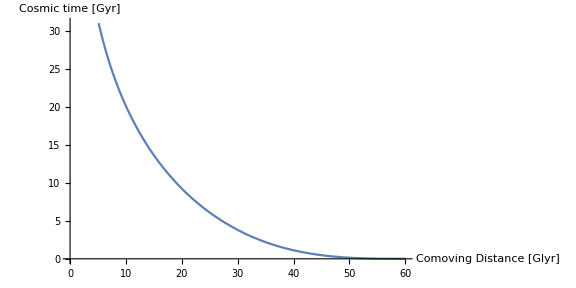

```mathematica
ParametricPlot[{NIntegrate[1/(a^2 √(Ωm a^-3+Ωl)),{a,x,∞}]*HubbleDistance*10^-2/3.2616,NIntegrate[1/(a √(Ωm a^-3+Ωl)),{a,0,x}]*HubbleTime},{x,0,3},AspectRatio->1/2,AxesLabel->{HoldForm["Comoving Distance [Glyr]"],HoldForm["Cosmic time [Gyr]"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->{{0,60},Automatic},ImageSize->Large,Ticks->{Range[0,60,10],Automatic}]
```

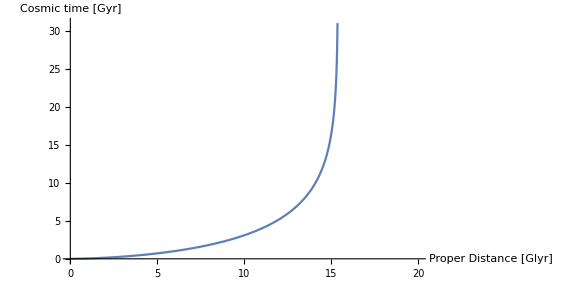

```mathematica
ParametricPlot[{x NIntegrate[1/(a^2 √(Ωm a^-3+Ωl)),{a,x,∞}]*HubbleDistance*10^-2/3.2616,NIntegrate[1/(a √(Ωm a^-3+Ωl)),{a,0,x}]*HubbleTime},{x,0,3},AspectRatio->1/2,AxesLabel->{HoldForm["Proper Distance [Glyr]"],HoldForm["Cosmic time [Gyr]"]}, LabelStyle->{FontFamily->"Comic Sans MS",15,GrayLevel[0]},PlotRange->{{0,20},Automatic},ImageSize->Large,Ticks->{Range[0,20,5],Automatic}]
```